```mathematica
ClearAll["Global`*"]
```

## Supplementary Material 2 : Quantum Thermal Rectification Under Non-Markovian Dynamics

This notebook includes the modelling and numerical evaluation of the behaviour of the quantum thermal diode model coupled to structured thermal baths.

### Pauli Matrices for Two-Level-System (Qubit)

```mathematica
Subscript[σ, x] = ({{0, 1}, {1, 0}}) ;
```

```mathematica
Subscript[σ, y] = ({{0, -ⅈ}, {ⅈ, 0}});
```

```mathematica
Subscript[σ, z] = ({{1, 0}, {0, -1}});
```

```mathematica
Subscript[σ, I] = ({{1, 0}, {0, 1}});
```

```mathematica
SubPlus[σ] =1/2*(Subscript[σ, x] + ⅈ*Subscript[σ, y]);
```

```mathematica
SubMinus[σ] =1/2*(Subscript[σ, x] - ⅈ*Subscript[σ, y]);
```

There are two energy states in a qubit and they can be described by two column vectors.

```mathematica
Subscript[z, 0]=Transpose[{{0,1}}];
Subscript[z, 1]=Transpose[{{1,0}}];
```

### Pauli Matrix Equivalents for Three-Level-System (Qutrit)

```mathematica
Subscript[ϕ, x] = ({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}) ;
Subscript[ϕ, y] = ({{0, -i, 0}, {i, 0, -i}, {0, i, 0}});
Subscript[ϕ, z] =({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
Subscript[ϕ, I] = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

There are three energy states in a qutrit and they can be described by three column vectors .

```mathematica
Subscript[Z, 0]=Transpose[{{0,0,1}}];
Subscript[Z, 1]=Transpose[{{0,1,0}}];
Subscript[Z, 2]=Transpose[{{1,0,0}}];
```

### Extended matrices for the 12-dimensional system

```mathematica
Subscript[σ, z,L]=KroneckerProduct[Subscript[σ, z],Subscript[ϕ, I],Subscript[σ, I]] ;
Subscript[σ, y,L]=KroneckerProduct[Subscript[σ, y],Subscript[ϕ, I],Subscript[σ, I]] ;
Subscript[σ, x,L]=KroneckerProduct[Subscript[σ, x],Subscript[ϕ, I],Subscript[σ, I]] ;
Subscript[σ, z,S0]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, z],Subscript[σ, I]] ;
Subscript[σ, y,S0]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, y],Subscript[σ, I]] ;
Subscript[σ, x,S0]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, x],Subscript[σ, I]] ;
Subscript[σ, z,R]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, I],Subscript[σ, z]] ;
Subscript[σ, y,R]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, I],Subscript[σ, y]] ;
Subscript[σ, x,R]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, I],Subscript[σ, x]] ;
```

```mathematica
Subscript[σ, Pos i_]:=Subscript[σ, Pos i]= 1/2*(Subscript[σ, x,i]+ ⅈ Subscript[σ, y,i]);
Subscript[σ, Neg i_]:=Subscript[σ, Neg i]= 1/2*(Subscript[σ, x,i]- ⅈ Subscript[σ, y,i]);
```

### System Hamiltonian

```mathematica
Σ=Subscript[z, 0].Subscript[z, 1] ᵀ;
```

```mathematica
Φ1=Subscript[Z, 0].Subscript[Z, 1] ᵀ;
Φ2=Subscript[Z, 1].Subscript[Z, 2] ᵀ;
```

```mathematica
Subscript[Σ, L]=KroneckerProduct[Σ,Subscript[ϕ, I],Subscript[σ, I]] ;
Subscript[Σ, 01]=KroneckerProduct[Subscript[σ, I],Φ1,Subscript[σ, I]] ;
Subscript[Σ, 12]=KroneckerProduct[Subscript[σ, I],Φ2,Subscript[σ, I]] ;
Subscript[Σ, R]=KroneckerProduct[Subscript[σ, I],Subscript[ϕ, I],Σ] ;
```

```mathematica
Subscript[H, L]=ℏ*Subscript[ω, L]*Subscript[Σ, L] ᵀ.Subscript[Σ, L];
Subscript[H, O]=ℏ*Subscript[ω, OL]*Subscript[Σ, 01] ᵀ.Subscript[Σ, 01]+ℏ*(Subscript[ω, OL]+Subscript[ω, OR])*Subscript[Σ, 12] ᵀ.Subscript[Σ, 12];
Subscript[H, R]=ℏ*Subscript[ω, R]*Subscript[Σ, R] ᵀ.Subscript[Σ, R];
Subscript[H, LO]=ℏ*Subscript[κ, L]*(Subscript[Σ, L].((Subscript[Σ, 01]+Subscript[Σ, 12])ᵀ)+(Subscript[Σ, L] ᵀ).(Subscript[Σ, 01]+Subscript[Σ, 12]));
Subscript[H, RO]=ℏ*Subscript[κ, R]*(Subscript[Σ, 12].(Subscript[Σ, R] ᵀ)+(Subscript[Σ, 12] ᵀ).Subscript[Σ, R]);
```

```mathematica
Subscript[H, SA]=Subscript[H, L]+Subscript[H, O]+Subscript[H, R]+Subscript[H, LO]+Subscript[H, RO];
```

```mathematica
MatrixForm[Subscript[H, SA]]
```

(ℏ ω_L+ℏ (ω_OL+ω_OR)+ℏ ω_R | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ ω_L+ℏ (ω_OL+ω_OR) | ℏ κ_R | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ κ_R | ℏ ω_L+ℏ ω_OL+ℏ ω_R | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ ω_L+ℏ ω_OL | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ ω_L+ℏ ω_R | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ ω_L | 0 | 0 | 0 | ℏ κ_L | 0 | 0
0 | 0 | ℏ κ_L | 0 | 0 | 0 | ℏ (ω_OL+ω_OR)+ℏ ω_R | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | ℏ (ω_OL+ω_OR) | ℏ κ_R | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | ℏ κ_R | ℏ ω_OL+ℏ ω_R | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | ℏ ω_OL | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_R | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[SparseH, SA]=SparseArray[FullSimplify[Subscript[H, SA]]];
```

```mathematica
MatrixForm[Subscript[SparseH, SA]]
```

(ℏ (ω_L+ω_OL+ω_OR+ω_R) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ (ω_L+ω_OL+ω_OR) | ℏ κ_R | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ κ_R | ℏ (ω_L+ω_OL+ω_R) | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ (ω_L+ω_OL) | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ (ω_L+ω_R) | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ ω_L | 0 | 0 | 0 | ℏ κ_L | 0 | 0
0 | 0 | ℏ κ_L | 0 | 0 | 0 | ℏ (ω_OL+ω_OR+ω_R) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | ℏ (ω_OL+ω_OR) | ℏ κ_R | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | ℏ κ_R | ℏ (ω_OL+ω_R) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ κ_L | 0 | 0 | 0 | ℏ ω_OL | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ ω_R | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{Eval,Evec}=Simplify[Eigensystem[Subscript[SparseH, SA]]];
SparseEvec=SparseArray[Evec];
EvecNormalized=Normalize/@SparseEvec;
list1=FullSimplify[Partition[Riffle[Eval,EvecNormalized],2]];
list1//MatrixForm
```

(0 | SparseArray[…]
ℏ Root[#1^3+κ_L^2 ω_L+κ_L^2 ω_OL+κ_R^2 ω_OL-ω_L^2 ω_OL-2 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR+κ_R^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-2 ω_OL^2 ω_OR-ω_L ω_OR^2-ω_OL ω_OR^2+#1^2 (-2 ω_L-3 ω_OL-2 ω_OR-2 ω_R)+κ_R^2 ω_R-ω_L^2 ω_R-3 ω_L ω_OL ω_R-2 ω_OL^2 ω_R-2 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_OR^2 ω_R-ω_L ω_R^2-ω_OL ω_R^2-ω_OR ω_R^2+#1 (-κ_L^2-κ_R^2+ω_L^2+4 ω_L ω_OL+3 ω_OL^2+3 ω_L ω_OR+4 ω_OL ω_OR+ω_OR^2+3 ω_L ω_R+4 ω_OL ω_R+3 ω_OR ω_R+ω_R^2)&,1] | SparseArray[…]
ℏ Root[#1^3+κ_L^2 ω_L+κ_L^2 ω_OL+κ_R^2 ω_OL-ω_L^2 ω_OL-2 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR+κ_R^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-2 ω_OL^2 ω_OR-ω_L ω_OR^2-ω_OL ω_OR^2+#1^2 (-2 ω_L-3 ω_OL-2 ω_OR-2 ω_R)+κ_R^2 ω_R-ω_L^2 ω_R-3 ω_L ω_OL ω_R-2 ω_OL^2 ω_R-2 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_OR^2 ω_R-ω_L ω_R^2-ω_OL ω_R^2-ω_OR ω_R^2+#1 (-κ_L^2-κ_R^2+ω_L^2+4 ω_L ω_OL+3 ω_OL^2+3 ω_L ω_OR+4 ω_OL ω_OR+ω_OR^2+3 ω_L ω_R+4 ω_OL ω_R+3 ω_OR ω_R+ω_R^2)&,2] | SparseArray[…]
ℏ Root[#1^3+κ_L^2 ω_L+κ_L^2 ω_OL+κ_R^2 ω_OL-ω_L^2 ω_OL-2 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR+κ_R^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-2 ω_OL^2 ω_OR-ω_L ω_OR^2-ω_OL ω_OR^2+#1^2 (-2 ω_L-3 ω_OL-2 ω_OR-2 ω_R)+κ_R^2 ω_R-ω_L^2 ω_R-3 ω_L ω_OL ω_R-2 ω_OL^2 ω_R-2 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_OR^2 ω_R-ω_L ω_R^2-ω_OL ω_R^2-ω_OR ω_R^2+#1 (-κ_L^2-κ_R^2+ω_L^2+4 ω_L ω_OL+3 ω_OL^2+3 ω_L ω_OR+4 ω_OL ω_OR+ω_OR^2+3 ω_L ω_R+4 ω_OL ω_R+3 ω_OR ω_R+ω_R^2)&,3] | SparseArray[…]
ℏ Root[#1^4+κ_L^4-κ_R^2 ω_L^2-2 κ_L^2 ω_L ω_OL-κ_R^2 ω_L ω_OL-κ_L^2 ω_OL^2+ω_L^2 ω_OL^2+ω_L ω_OL^3-κ_L^2 ω_L ω_OR-κ_L^2 ω_OL ω_OR+ω_L^2 ω_OL ω_OR+ω_L ω_OL^2 ω_OR+#1^3 (-2 ω_L-3 ω_OL-ω_OR-2 ω_R)-κ_L^2 ω_L ω_R-κ_R^2 ω_L ω_R-κ_L^2 ω_OL ω_R-κ_R^2 ω_OL ω_R+ω_L^2 ω_OL ω_R+2 ω_L ω_OL^2 ω_R+ω_OL^3 ω_R+ω_L^2 ω_OR ω_R+2 ω_L ω_OL ω_OR ω_R+ω_OL^2 ω_OR ω_R-κ_L^2 ω_R^2+ω_L ω_OL ω_R^2+ω_OL^2 ω_R^2+ω_L ω_OR ω_R^2+ω_OL ω_OR ω_R^2+#1^2 (-2 κ_L^2-κ_R^2+ω_L^2+5 ω_L ω_OL+3 ω_OL^2+2 ω_L ω_OR+2 ω_OL ω_OR+3 ω_L ω_R+5 ω_OL ω_R+2 ω_OR ω_R+ω_R^2)+#1 (2 κ_L^2 ω_L+2 κ_R^2 ω_L+3 κ_L^2 ω_OL+κ_R^2 ω_OL-2 ω_L^2 ω_OL-4 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-ω_OL^2 ω_OR+2 κ_L^2 ω_R+κ_R^2 ω_R-ω_L^2 ω_R-5 ω_L ω_OL ω_R-4 ω_OL^2 ω_R-3 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_L ω_R^2-2 ω_OL ω_R^2-ω_OR ω_R^2)&,1] | SparseArray[…]
ℏ Root[#1^4+κ_L^4-κ_R^2 ω_L^2-2 κ_L^2 ω_L ω_OL-κ_R^2 ω_L ω_OL-κ_L^2 ω_OL^2+ω_L^2 ω_OL^2+ω_L ω_OL^3-κ_L^2 ω_L ω_OR-κ_L^2 ω_OL ω_OR+ω_L^2 ω_OL ω_OR+ω_L ω_OL^2 ω_OR+#1^3 (-2 ω_L-3 ω_OL-ω_OR-2 ω_R)-κ_L^2 ω_L ω_R-κ_R^2 ω_L ω_R-κ_L^2 ω_OL ω_R-κ_R^2 ω_OL ω_R+ω_L^2 ω_OL ω_R+2 ω_L ω_OL^2 ω_R+ω_OL^3 ω_R+ω_L^2 ω_OR ω_R+2 ω_L ω_OL ω_OR ω_R+ω_OL^2 ω_OR ω_R-κ_L^2 ω_R^2+ω_L ω_OL ω_R^2+ω_OL^2 ω_R^2+ω_L ω_OR ω_R^2+ω_OL ω_OR ω_R^2+#1^2 (-2 κ_L^2-κ_R^2+ω_L^2+5 ω_L ω_OL+3 ω_OL^2+2 ω_L ω_OR+2 ω_OL ω_OR+3 ω_L ω_R+5 ω_OL ω_R+2 ω_OR ω_R+ω_R^2)+#1 (2 κ_L^2 ω_L+2 κ_R^2 ω_L+3 κ_L^2 ω_OL+κ_R^2 ω_OL-2 ω_L^2 ω_OL-4 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-ω_OL^2 ω_OR+2 κ_L^2 ω_R+κ_R^2 ω_R-ω_L^2 ω_R-5 ω_L ω_OL ω_R-4 ω_OL^2 ω_R-3 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_L ω_R^2-2 ω_OL ω_R^2-ω_OR ω_R^2)&,2] | SparseArray[…]
ℏ Root[#1^4+κ_L^4-κ_R^2 ω_L^2-2 κ_L^2 ω_L ω_OL-κ_R^2 ω_L ω_OL-κ_L^2 ω_OL^2+ω_L^2 ω_OL^2+ω_L ω_OL^3-κ_L^2 ω_L ω_OR-κ_L^2 ω_OL ω_OR+ω_L^2 ω_OL ω_OR+ω_L ω_OL^2 ω_OR+#1^3 (-2 ω_L-3 ω_OL-ω_OR-2 ω_R)-κ_L^2 ω_L ω_R-κ_R^2 ω_L ω_R-κ_L^2 ω_OL ω_R-κ_R^2 ω_OL ω_R+ω_L^2 ω_OL ω_R+2 ω_L ω_OL^2 ω_R+ω_OL^3 ω_R+ω_L^2 ω_OR ω_R+2 ω_L ω_OL ω_OR ω_R+ω_OL^2 ω_OR ω_R-κ_L^2 ω_R^2+ω_L ω_OL ω_R^2+ω_OL^2 ω_R^2+ω_L ω_OR ω_R^2+ω_OL ω_OR ω_R^2+#1^2 (-2 κ_L^2-κ_R^2+ω_L^2+5 ω_L ω_OL+3 ω_OL^2+2 ω_L ω_OR+2 ω_OL ω_OR+3 ω_L ω_R+5 ω_OL ω_R+2 ω_OR ω_R+ω_R^2)+#1 (2 κ_L^2 ω_L+2 κ_R^2 ω_L+3 κ_L^2 ω_OL+κ_R^2 ω_OL-2 ω_L^2 ω_OL-4 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-ω_OL^2 ω_OR+2 κ_L^2 ω_R+κ_R^2 ω_R-ω_L^2 ω_R-5 ω_L ω_OL ω_R-4 ω_OL^2 ω_R-3 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_L ω_R^2-2 ω_OL ω_R^2-ω_OR ω_R^2)&,3] | SparseArray[…]
ℏ Root[#1^4+κ_L^4-κ_R^2 ω_L^2-2 κ_L^2 ω_L ω_OL-κ_R^2 ω_L ω_OL-κ_L^2 ω_OL^2+ω_L^2 ω_OL^2+ω_L ω_OL^3-κ_L^2 ω_L ω_OR-κ_L^2 ω_OL ω_OR+ω_L^2 ω_OL ω_OR+ω_L ω_OL^2 ω_OR+#1^3 (-2 ω_L-3 ω_OL-ω_OR-2 ω_R)-κ_L^2 ω_L ω_R-κ_R^2 ω_L ω_R-κ_L^2 ω_OL ω_R-κ_R^2 ω_OL ω_R+ω_L^2 ω_OL ω_R+2 ω_L ω_OL^2 ω_R+ω_OL^3 ω_R+ω_L^2 ω_OR ω_R+2 ω_L ω_OL ω_OR ω_R+ω_OL^2 ω_OR ω_R-κ_L^2 ω_R^2+ω_L ω_OL ω_R^2+ω_OL^2 ω_R^2+ω_L ω_OR ω_R^2+ω_OL ω_OR ω_R^2+#1^2 (-2 κ_L^2-κ_R^2+ω_L^2+5 ω_L ω_OL+3 ω_OL^2+2 ω_L ω_OR+2 ω_OL ω_OR+3 ω_L ω_R+5 ω_OL ω_R+2 ω_OR ω_R+ω_R^2)+#1 (2 κ_L^2 ω_L+2 κ_R^2 ω_L+3 κ_L^2 ω_OL+κ_R^2 ω_OL-2 ω_L^2 ω_OL-4 ω_L ω_OL^2-ω_OL^3+κ_L^2 ω_OR-ω_L^2 ω_OR-3 ω_L ω_OL ω_OR-ω_OL^2 ω_OR+2 κ_L^2 ω_R+κ_R^2 ω_R-ω_L^2 ω_R-5 ω_L ω_OL ω_R-4 ω_OL^2 ω_R-3 ω_L ω_OR ω_R-3 ω_OL ω_OR ω_R-ω_L ω_R^2-2 ω_OL ω_R^2-ω_OR ω_R^2)&,4] | SparseArray[…]
1/2 ℏ (ω_L-√(4 κ_L^2+(ω_L-ω_OL)^2)+ω_OL) | SparseArray[…]
1/2 ℏ (ω_L+√(4 κ_L^2+(ω_L-ω_OL)^2)+ω_OL) | SparseArray[…]
ℏ ω_R | SparseArray[…]
ℏ (ω_L+ω_OL+ω_OR+ω_R) | SparseArray[…])

system states and their energies

```mathematica
Subscript[λ, i_]:=Subscript[λ, i]=Transpose[{list1[[i]][[2]]}]
```

```mathematica
HsEVal=Table[list1[[i]][[1]],{i,1,12}]//MatrixForm;
```

## Quantum Master Equation

### Density Matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}];
MatrixForm[%]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t] | ρ_(1,7)[t] | ρ_(1,8)[t] | ρ_(1,9)[t] | ρ_(1,10)[t] | ρ_(1,11)[t] | ρ_(1,12)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t] | ρ_(2,7)[t] | ρ_(2,8)[t] | ρ_(2,9)[t] | ρ_(2,10)[t] | ρ_(2,11)[t] | ρ_(2,12)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t] | ρ_(3,7)[t] | ρ_(3,8)[t] | ρ_(3,9)[t] | ρ_(3,10)[t] | ρ_(3,11)[t] | ρ_(3,12)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t] | ρ_(4,7)[t] | ρ_(4,8)[t] | ρ_(4,9)[t] | ρ_(4,10)[t] | ρ_(4,11)[t] | ρ_(4,12)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t] | ρ_(5,7)[t] | ρ_(5,8)[t] | ρ_(5,9)[t] | ρ_(5,10)[t] | ρ_(5,11)[t] | ρ_(5,12)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t] | ρ_(6,7)[t] | ρ_(6,8)[t] | ρ_(6,9)[t] | ρ_(6,10)[t] | ρ_(6,11)[t] | ρ_(6,12)[t]
ρ_(7,1)[t] | ρ_(7,2)[t] | ρ_(7,3)[t] | ρ_(7,4)[t] | ρ_(7,5)[t] | ρ_(7,6)[t] | ρ_(7,7)[t] | ρ_(7,8)[t] | ρ_(7,9)[t] | ρ_(7,10)[t] | ρ_(7,11)[t] | ρ_(7,12)[t]
ρ_(8,1)[t] | ρ_(8,2)[t] | ρ_(8,3)[t] | ρ_(8,4)[t] | ρ_(8,5)[t] | ρ_(8,6)[t] | ρ_(8,7)[t] | ρ_(8,8)[t] | ρ_(8,9)[t] | ρ_(8,10)[t] | ρ_(8,11)[t] | ρ_(8,12)[t]
ρ_(9,1)[t] | ρ_(9,2)[t] | ρ_(9,3)[t] | ρ_(9,4)[t] | ρ_(9,5)[t] | ρ_(9,6)[t] | ρ_(9,7)[t] | ρ_(9,8)[t] | ρ_(9,9)[t] | ρ_(9,10)[t] | ρ_(9,11)[t] | ρ_(9,12)[t]
ρ_(10,1)[t] | ρ_(10,2)[t] | ρ_(10,3)[t] | ρ_(10,4)[t] | ρ_(10,5)[t] | ρ_(10,6)[t] | ρ_(10,7)[t] | ρ_(10,8)[t] | ρ_(10,9)[t] | ρ_(10,10)[t] | ρ_(10,11)[t] | ρ_(10,12)[t]
ρ_(11,1)[t] | ρ_(11,2)[t] | ρ_(11,3)[t] | ρ_(11,4)[t] | ρ_(11,5)[t] | ρ_(11,6)[t] | ρ_(11,7)[t] | ρ_(11,8)[t] | ρ_(11,9)[t] | ρ_(11,10)[t] | ρ_(11,11)[t] | ρ_(11,12)[t]
ρ_(12,1)[t] | ρ_(12,2)[t] | ρ_(12,3)[t] | ρ_(12,4)[t] | ρ_(12,5)[t] | ρ_(12,6)[t] | ρ_(12,7)[t] | ρ_(12,8)[t] | ρ_(12,9)[t] | ρ_(12,10)[t] | ρ_(12,11)[t] | ρ_(12,12)[t])

### Possible Transition Frequencies

```mathematica
ωMatrix={Flatten[Table[Subscript[ω, {i,j}],{i,1,12},{j,i+1,12}]]}
```

{{ω_{1,2},ω_{1,3},ω_{1,4},ω_{1,5},ω_{1,6},ω_{1,7},ω_{1,8},ω_{1,9},ω_{1,10},ω_{1,11},ω_{1,12},ω_{2,3},ω_{2,4},ω_{2,5},ω_{2,6},ω_{2,7},ω_{2,8},ω_{2,9},ω_{2,10},ω_{2,11},ω_{2,12},ω_{3,4},ω_{3,5},ω_{3,6},ω_{3,7},ω_{3,8},ω_{3,9},ω_{3,10},ω_{3,11},ω_{3,12},ω_{4,5},ω_{4,6},ω_{4,7},ω_{4,8},ω_{4,9},ω_{4,10},ω_{4,11},ω_{4,12},ω_{5,6},ω_{5,7},ω_{5,8},ω_{5,9},ω_{5,10},ω_{5,11},ω_{5,12},ω_{6,7},ω_{6,8},ω_{6,9},ω_{6,10},ω_{6,11},ω_{6,12},ω_{7,8},ω_{7,9},ω_{7,10},ω_{7,11},ω_{7,12},ω_{8,9},ω_{8,10},ω_{8,11},ω_{8,12},ω_{9,10},ω_{9,11},ω_{9,12},ω_{10,11},ω_{10,12},ω_{11,12}}}

```mathematica
ωVals=Flatten[Simplify[Table[(HsEVal[[1,j]]-HsEVal[[1,i]])/ℏ,{i,1,12},{j,i+1,12}]]];
```

```mathematica
Dimensions[ωVals]
```

{66}

### Lindblad Dissipator

```mathematica
Subscript[ℒ, L]=Subscript[g, L]^2(1-Subscript[n, L][Subscript[ω, L]])(Subscript[Σ, L].ρMatrix[t].Subscript[Σ, L] ᵀ-1/2 Subscript[Σ, L] ᵀ.Subscript[Σ, L].ρMatrix[t]-1/2 ρMatrix[t].Subscript[Σ, L] ᵀ.Subscript[Σ, L])+(Subscript[g, L]^2 Subscript[n, L][Subscript[ω, L]](Subscript[Σ, L] ᵀ.ρMatrix[t].Subscript[Σ, L]-1/2 Subscript[Σ, L].Subscript[Σ, L] ᵀ.ρMatrix[t]-1/2 ρMatrix[t].Subscript[Σ, L].Subscript[Σ, L] ᵀ));
```

```mathematica
Subscript[ℒ, R]=Subscript[g, R]^2(1-Subscript[n, R][Subscript[ω, R]])(Subscript[Σ, R].ρMatrix[t].Subscript[Σ, R] ᵀ-1/2 Subscript[Σ, R] ᵀ.Subscript[Σ, R].ρMatrix[t]-1/2 ρMatrix[t].Subscript[Σ, R] ᵀ.Subscript[Σ, R])+(Subscript[g, R]^2 Subscript[n, R][Subscript[ω, R]](Subscript[Σ, R] ᵀ.ρMatrix[t].Subscript[Σ, R]-1/2 Subscript[Σ, R].Subscript[Σ, R] ᵀ.ρMatrix[t]-1/2 ρMatrix[t].Subscript[Σ, R].Subscript[Σ, R] ᵀ));
```

### Master Equation

```mathematica
dρ=MatrixForm[Subscript[ℒ, L]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[SparseH, SA].ρMatrix[t]-ρMatrix[t].Subscript[SparseH, SA]))]
```

## Solving Master Equation

```mathematica
NBEassum=Subscript[n, q_][ω_]-> 1/(ⅇ^((ℏ ω)/(Subscript[k, B] Subscript[T, q]))+1);
```

### Solving Master Equation

```mathematica
RHS=Subscript[ℒ, L]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[SparseH, SA].ρMatrix[t]-ρMatrix[t].Subscript[SparseH, SA]));
```

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t] | ρ_(1,5)'[t] | ρ_(1,6)'[t] | ρ_(1,7)'[t] | ρ_(1,8)'[t] | ρ_(1,9)'[t] | ρ_(1,10)'[t] | ρ_(1,11)'[t] | ρ_(1,12)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t] | ρ_(2,5)'[t] | ρ_(2,6)'[t] | ρ_(2,7)'[t] | ρ_(2,8)'[t] | ρ_(2,9)'[t] | ρ_(2,10)'[t] | ρ_(2,11)'[t] | ρ_(2,12)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t] | ρ_(3,5)'[t] | ρ_(3,6)'[t] | ρ_(3,7)'[t] | ρ_(3,8)'[t] | ρ_(3,9)'[t] | ρ_(3,10)'[t] | ρ_(3,11)'[t] | ρ_(3,12)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t] | ρ_(4,5)'[t] | ρ_(4,6)'[t] | ρ_(4,7)'[t] | ρ_(4,8)'[t] | ρ_(4,9)'[t] | ρ_(4,10)'[t] | ρ_(4,11)'[t] | ρ_(4,12)'[t]
ρ_(5,1)'[t] | ρ_(5,2)'[t] | ρ_(5,3)'[t] | ρ_(5,4)'[t] | ρ_(5,5)'[t] | ρ_(5,6)'[t] | ρ_(5,7)'[t] | ρ_(5,8)'[t] | ρ_(5,9)'[t] | ρ_(5,10)'[t] | ρ_(5,11)'[t] | ρ_(5,12)'[t]
ρ_(6,1)'[t] | ρ_(6,2)'[t] | ρ_(6,3)'[t] | ρ_(6,4)'[t] | ρ_(6,5)'[t] | ρ_(6,6)'[t] | ρ_(6,7)'[t] | ρ_(6,8)'[t] | ρ_(6,9)'[t] | ρ_(6,10)'[t] | ρ_(6,11)'[t] | ρ_(6,12)'[t]
ρ_(7,1)'[t] | ρ_(7,2)'[t] | ρ_(7,3)'[t] | ρ_(7,4)'[t] | ρ_(7,5)'[t] | ρ_(7,6)'[t] | ρ_(7,7)'[t] | ρ_(7,8)'[t] | ρ_(7,9)'[t] | ρ_(7,10)'[t] | ρ_(7,11)'[t] | ρ_(7,12)'[t]
ρ_(8,1)'[t] | ρ_(8,2)'[t] | ρ_(8,3)'[t] | ρ_(8,4)'[t] | ρ_(8,5)'[t] | ρ_(8,6)'[t] | ρ_(8,7)'[t] | ρ_(8,8)'[t] | ρ_(8,9)'[t] | ρ_(8,10)'[t] | ρ_(8,11)'[t] | ρ_(8,12)'[t]
ρ_(9,1)'[t] | ρ_(9,2)'[t] | ρ_(9,3)'[t] | ρ_(9,4)'[t] | ρ_(9,5)'[t] | ρ_(9,6)'[t] | ρ_(9,7)'[t] | ρ_(9,8)'[t] | ρ_(9,9)'[t] | ρ_(9,10)'[t] | ρ_(9,11)'[t] | ρ_(9,12)'[t]
ρ_(10,1)'[t] | ρ_(10,2)'[t] | ρ_(10,3)'[t] | ρ_(10,4)'[t] | ρ_(10,5)'[t] | ρ_(10,6)'[t] | ρ_(10,7)'[t] | ρ_(10,8)'[t] | ρ_(10,9)'[t] | ρ_(10,10)'[t] | ρ_(10,11)'[t] | ρ_(10,12)'[t]
ρ_(11,1)'[t] | ρ_(11,2)'[t] | ρ_(11,3)'[t] | ρ_(11,4)'[t] | ρ_(11,5)'[t] | ρ_(11,6)'[t] | ρ_(11,7)'[t] | ρ_(11,8)'[t] | ρ_(11,9)'[t] | ρ_(11,10)'[t] | ρ_(11,11)'[t] | ρ_(11,12)'[t]
ρ_(12,1)'[t] | ρ_(12,2)'[t] | ρ_(12,3)'[t] | ρ_(12,4)'[t] | ρ_(12,5)'[t] | ρ_(12,6)'[t] | ρ_(12,7)'[t] | ρ_(12,8)'[t] | ρ_(12,9)'[t] | ρ_(12,10)'[t] | ρ_(12,11)'[t] | ρ_(12,12)'[t])

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,12},{j,1,12}]]]/.Rule->Equal];
```

```mathematica
ωassum1=Flatten[{Table[Subscript[ω, {i,j}]->(-(HsEVal[[1,i]]-HsEVal[[1,j]]))/ℏ,{i,1,12},{j,1,12}]}];
ωassum2={Table[Subscript[ω, i]-> HsEVal[[1,i]]/ℏ,{i,1,12}]};
unitassum = {Subscript[k, B]-> 1,ℏ->1};
tmax=5;
```

### Initial Conditions

```mathematica
Subscript[ρo, i_]:=Subscript[ρo, i]=Exp[-(ℏ*Subscript[ω, i]*Σᵀ.Σ)/Subscript[T, i]]/Tr[Exp[-(ℏ*Subscript[ω, i]*Σᵀ.Σ)/Subscript[T, i]]];
```

```mathematica
Subscript[ρo, S0]={{0,0,0},{0,0,0},{0,0,1}};
Subscript[ρo, S2]={{1,0,0},{0,0,0},{0,0,0}};
```

### System Parameters for Forward and Reverse Conditions

Forward Condition T_L>T_R

```mathematica
Subscript[Tassum, 1]={Subscript[ω, OL]->3,Subscript[ω, OR]->3,Subscript[ω, L] ->3,Subscript[ω, R] ->3,Subscript[T, R]->0.5 Subscript[ω, L],Subscript[T, L]->5 Subscript[ω, R],Subscript[g, L]->0.5 Subscript[ω, L] ,Subscript[g, R]->0.5 Subscript[ω, R],Subscript[κ, L]->1*Subscript[g, L],Subscript[κ, R]->1*Subscript[g, R]};
Subscript[Tassum, 5]={Subscript[ω, OL]->3,Subscript[ω, OR]->3,Subscript[ω, L] ->3,Subscript[ω, R] ->3,Subscript[T, R]->0.5 Subscript[ω, R],Subscript[T, L]->5 Subscript[ω, L],Subscript[g, L]->0.5 Subscript[ω, L] ,Subscript[g, R]->0.5 Subscript[ω, R],Subscript[κ, L]->5*Subscript[g, L],Subscript[κ, R]->5*Subscript[g, R]};
Subscript[Tassum, 10]={Subscript[ω, OL]->3,Subscript[ω, OR]->3,Subscript[ω, L] ->3,Subscript[ω, R] ->3,Subscript[T, R]->0.5 Subscript[ω, R],Subscript[T, L]->5 Subscript[ω, L],Subscript[g, L]->0.5 Subscript[ω, L] ,Subscript[g, R]->0.5 Subscript[ω, R],Subscript[κ, L]->10*Subscript[g, L],Subscript[κ, R]->10*Subscript[g, R]};
```

Reverse Condition T_R>T_L

```mathematica
Subscript[Tassum, R1]={Subscript[ω, OL]->3,Subscript[ω, OR]->3,Subscript[ω, L] ->3,Subscript[ω, R] ->3,Subscript[T, R]->5 Subscript[ω, L],Subscript[T, L]->0.5 Subscript[ω, R],Subscript[g, L]->0.5 Subscript[ω, L] ,Subscript[g, R]->0.5 Subscript[ω, R],Subscript[κ, L]->1*Subscript[g, L],Subscript[κ, R]->1*Subscript[g, R]};
Subscript[Tassum, R5]={Subscript[ω, OL]->3,Subscript[ω, OR]->3,Subscript[ω, L] ->3,Subscript[ω, R] ->3,Subscript[T, R]->5 Subscript[ω, R],Subscript[T, L]->0.5 Subscript[ω, L],Subscript[g, L]->0.5 Subscript[ω, L] ,Subscript[g, R]->0.5 Subscript[ω, R],Subscript[κ, L]->5*Subscript[g, L],Subscript[κ, R]->5*Subscript[g, R]};
Subscript[Tassum, R10]={Subscript[ω, OL]->3,Subscript[ω, OR]->3,Subscript[ω, L] ->3,Subscript[ω, R] ->3,Subscript[T, R]->5 Subscript[ω, R],Subscript[T, L]->0.5 Subscript[ω, L],Subscript[g, L]->0.5 Subscript[ω, L] ,Subscript[g, R]->0.5 Subscript[ω, R],Subscript[κ, L]->10*Subscript[g, L],Subscript[κ, R]->10*Subscript[g, R]};
```

### Solution

Initial conditions with system parameters

```mathematica
Subscript[RHSρoS, 0,λ_]:=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S0],Subscript[ρo, R]]//.Flatten[{Subscript[Tassum, λ],unitassum}];(* when qutrit is in Subscript[ρo, S0] *)
Subscript[RHSρoS, 2,λ_]:=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S2],Subscript[ρo, R]]//.Flatten[{Subscript[Tassum, λ],unitassum}];(* when qutrit is in Subscript[ρo, S2] *)
```

Set of differential equations with system parameters

```mathematica
Subscript[sol, λ_]:=sol//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
Subscript[simplifiedSol, λ_]:=Subscript[sol, λ]//.{Exp[x_?Negative]/;Abs[x]>10^6->0};
```

Solving  differential  equations

```mathematica
Subscript[dynamics, ini_,λ_]:=NDSolve[Flatten[{Subscript[simplifiedSol, λ]//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}],N[Table[Subscript[ρ, i,j][0]==Subscript[RHSρoS, ini,λ][[i,j]],{i,1,12},{j,1,12}]]}],Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}];
```

Density matrix diagonal elements

```mathematica
Subscript[Diag, ini_,λ_]:=Flatten[{Table[Subscript[ρ, i,i][t],{i,1,12}]}/. Subscript[dynamics, ini,λ]];
```

Density matrix off-diagonals

```mathematica
Subscript[OffDiag, ini_,λ_]:=Flatten@Table[If[i!=j,Subscript[ρ, i,j][t],Nothing],{i,1,12},{j,1,12}]/. Subscript[dynamics, ini,λ];
```

## Results

### Density Matrix Element Dynamics

plot density matrix diagonals

```mathematica
Subscript[PlotDiagonal, ini_,λ_]:=Plot[Evaluate[Subscript[Diag, ini,λ]],{t,0,5},PlotRange-> All,PlotLabel->  Style["κ/g=" <> ToString[λ]],AxesLabel->{Style["t"],Style["Probability"]}, 
PlotLegends->Flatten[{Table[Subscript[ρ, i,i][t],{i,1,12}]}],ImageSize->Medium]
```

plot density matrix off-diagonals

```mathematica
Subscript[PlotOffDiagonal1, ini_,λ_]:=Plot[Evaluate[Subscript[OffDiag, ini,λ][[1]][[{17,41,51,65}]]],{t,0,5},PlotRange-> All,PlotLabel->  Style["κ/g=" <> ToString[λ]],AxesLabel->{Style["t"],Style["Coherence"]}, 
PlotLegends->{"ρ_(2, 7)[t],ρ_(7, 2)[t]","ρ_(4, 9)[t],ρ_(9, 4)[t]","ρ_(5, 8)[t],ρ_(8, 5)[t]","ρ_(6, 11)[t],ρ_(11, 6)[t]"},ImageSize->Medium]
(*Subscript[PlotOffDiagonal2, ini_,λ_]:=Plot[Evaluate[Subscript[OffDiag, ini,λ][[1]][[{68,82,92,116}]]],{t,0,5},PlotRange-> All,PlotLabel->  Style["κ/g=" <> ToString[λ]],AxesLabel->{Style["t(s)"],Style["Coherence"]}, 
PlotLegends->{"ρ_(7, 2)[t]","ρ_(8, 5)[t]","ρ_(9, 4)[t]","ρ_(11, 6)[t]"},ImageSize->Medium]*)
```

### 1.a) probabilities in forward condition

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsRow[{Subscript[PlotDiagonal, 0,1],Subscript[PlotDiagonal, 0,5],Subscript[PlotDiagonal, 0,10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Diagonals - Forward Condition - Initial Condition 1",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsRow[{Subscript[PlotDiagonal, 2,1],Subscript[PlotDiagonal, 2,5],Subscript[PlotDiagonal, 2,10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Diagonals - Forward Condition - Initial Condition 2",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

### 1.b) Coherence in forward condition

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsGrid[{{Subscript[PlotOffDiagonal1, 0,1],Subscript[PlotOffDiagonal1, 0,5],Subscript[PlotOffDiagonal1, 0,10]}(*,{Subscript[PlotOffDiagonal2, 0,1],Subscript[PlotOffDiagonal2, 0,5],Subscript[PlotOffDiagonal2, 0,25]}*)},ImageSize->Full,Epilog->Inset[Style["Density Matrix Off-Diagonals - Forward Condition - Initial Condition 1",13,Bold],Scaled[{0.5,1.35}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsGrid[{{Subscript[PlotOffDiagonal1, 2,1],Subscript[PlotOffDiagonal1, 2,5],Subscript[PlotOffDiagonal1, 2,10]}(*,{Subscript[PlotOffDiagonal2, 2,1],Subscript[PlotOffDiagonal2, 2,5],Subscript[PlotOffDiagonal2, 2,25]}*)},ImageSize->Full,Epilog->Inset[Style["Density Matrix Off-Diagonals - Forward Condition - Initial Condition 1",13,Bold],Scaled[{0.5,1.35}]]]
```

-Graphics-

### 2.a) probabilities in reverse condition

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsRow[{Subscript[PlotDiagonal, 0,R1],Subscript[PlotDiagonal, 0,R5],Subscript[PlotDiagonal, 0,R10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Diagonals - Forward Condition - Initial Condition 1",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsRow[{Subscript[PlotDiagonal, 2,R1],Subscript[PlotDiagonal, 2,R5],Subscript[PlotDiagonal, 2,R10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Diagonals - Forward Condition - Initial Condition 2",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

### 2.b) Coherence in reverse condition

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsGrid[{{Subscript[PlotOffDiagonal1, 0,R1],Subscript[PlotOffDiagonal1, 0,R5],Subscript[PlotOffDiagonal1, 0,R10]}(*,{Subscript[PlotOffDiagonal2, 0,R1],Subscript[PlotOffDiagonal2, 0,R5],Subscript[PlotOffDiagonal2, 0,R25]}*)},ImageSize->Full,Epilog->Inset[Style["Density Matrix Off-Diagonals - Reverse Condition - Initial Condition 1",13,Bold],Scaled[{0.5,1.35}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsGrid[{{Subscript[PlotOffDiagonal1, 2,R1],Subscript[PlotOffDiagonal1, 2,R5],Subscript[PlotOffDiagonal1, 2,R10]}(*,{Subscript[PlotOffDiagonal2, 2,R1],Subscript[PlotOffDiagonal2, 2,R5],Subscript[PlotOffDiagonal2, 2,R25]}*)},ImageSize->Full,Epilog->Inset[Style["Density Matrix Off-Diagonals - Reverse Condition - Initial Condition 1",13,Bold],Scaled[{0.5,1.35}]]]
```

-Graphics-

### Qutrit populations derived using partial trace

```mathematica
HQubit=ℏ*Subscript[ω, OL]*Φ1ᵀ.Φ1+ℏ*(Subscript[ω, OL]+Subscript[ω, OR])*Φ2ᵀ.Φ2;
HLQubit=ℏ*Subscript[ω, L]*Σᵀ.Σ;
HRQubit=ℏ*Subscript[ω, R]*Σᵀ.Σ;
```

```mathematica
Subscript[mat, ini_,λ_][t_]:=Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}]/. Subscript[dynamics, ini,λ]
Subscript[ρSLMatrix, ini_,λ_]:=Flatten[ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{2,3},{2,3,2}]];
Subscript[ρSOMatrix, ini_,λ_]:=Flatten[ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{1,3},{2,3,2}]];
Subscript[ρSRMatrix, ini_,λ_]:=Flatten[ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{1,2},{2,3,2}]];
```

```mathematica
Subscript[ρSOMatrixMatrix, ini_,λ_]:=ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{1,3},{2,3,2}];
Subscript[ρSLMatrixMatrix, ini_,λ_]:=ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{2,3},{2,3,2}];
Subscript[ρSRMatrixMatrix, ini_,λ_]:=ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{1,2},{2,3,2}];
```

```mathematica
Subscript[QutritDiagonalPlot, ini_,λ_]:=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, ini,λ]]],{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotLegends->Placed[{Style["ρ_(|2⟩)",13],Style["ρ_(|1⟩)",13],Style["ρ_(|0⟩)",13]},Bottom],PlotLabel->  Style["κ/g=" <> ToString[λ],15],ImageSize->Medium];
```

### 1) in forward condition

With initial condition 1 - RHSρoS_0

```mathematica
Subscript[QutritDiagonalPlot1, 0,1]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 0,1]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dotted,Green},{Dotted,Blue},{Dotted,Red}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 0,5]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 0,5]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dashed,Darker[Green]},{Dashed,Darker[Blue]},{Dashed,Darker[Red]}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 0,10]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 0,10]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{Lighter[Green],Lighter[Blue],Lighter[Red]},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 0]=Show[Subscript[QutritDiagonalPlot1, 0,1],Subscript[QutritDiagonalPlot1, 0,5],Subscript[QutritDiagonalPlot1, 0,10],ImageSize->All];
```

With initial condition 2 - RHSρoS_2

```mathematica
Subscript[QutritDiagonalPlot1, 2,1]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 2,1]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dotted,Green},{Dotted,Blue},{Dotted,Red}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 2,5]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 2,5]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dashed,Darker[Green]},{Dashed,Darker[Blue]},{Dashed,Darker[Red]}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 2,10]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 2,10]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{Lighter[Green],Lighter[Blue],Lighter[Red]},ImageSize->Large];Subscript[QutritDiagonalPlot1, 2]=Show[Subscript[QutritDiagonalPlot1, 2,1],Subscript[QutritDiagonalPlot1, 2,5],Subscript[QutritDiagonalPlot1, 2,10],ImageSize->All];
```

Legend for plots

```mathematica
Lgnd=Grid[{{Style["κ/g=1",15],Style["κ/g=5",15],Style["κ/g=10",15]},
{Row[{Graphics[{Darker[Green],Dotted,Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|0⟩)",14]}],
Row[{Graphics[{Darker[Green],Dashed,Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|0⟩)",14]}],
Row[{Graphics[{Lighter[Green],Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|0⟩)",14]}]},
{Row[{Graphics[{Blue,Dotted,Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|1⟩)",14]}],
Row[{Graphics[{Darker[Blue],Dashed,Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|1⟩)",14]}],
Row[{Graphics[{Lighter[Blue],Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|1⟩)",14]}]},
{Row[{Graphics[{Red,Dotted,Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|2⟩)",14]}],
Row[{Graphics[{Darker[Red],Dashed,Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|2⟩)",14]}],
Row[{Graphics[{Lighter[Red],Line[{{0,0},{0.3,0}}]},ImageSize->{30,10},AspectRatio->0.01],Style[" ρ_(|2⟩)",14]}]}},Frame->All,FrameStyle->Gray,Spacings->{3.3, 0.5},Background->Lighter[Lighter[Gray], 0.8]];
```

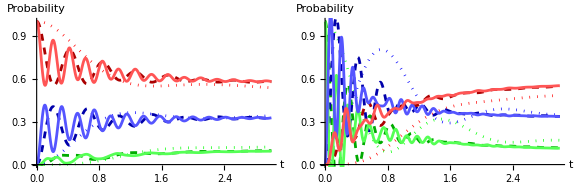

```mathematica
GraphicsGrid[{{Subscript[QutritDiagonalPlot1, 0],Subscript[QutritDiagonalPlot1, 2]},{Lgnd,SpanFromLeft}},Spacings->{1,0},ImageSize->Large]
```

### 2) in reverse condition

With initial condition 1 - RHSρoS_0

```mathematica
Subscript[QutritDiagonalPlot1, 0,R1]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 0,R1]]],{t,0,1.5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dotted,Green},{Dotted,Blue},{Dotted,Red}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 0,R5]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 0,R5]]],{t,0,1.5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dashed,Darker[Green]},{Dashed,Darker[Blue]},{Dashed,Darker[Red]}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 0,R10]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 0,R10]]],{t,0,1.5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{Lighter[Green],Lighter[Blue],Lighter[Red]},ImageSize->Large];
Subscript[QutritDiagonalPlot1, R0]=Show[Subscript[QutritDiagonalPlot1, 0,R1],Subscript[QutritDiagonalPlot1, 0,R5],Subscript[QutritDiagonalPlot1, 0,R10],ImageSize->All];
```

With initial condition 2 - RHSρoS_2

```mathematica
Subscript[QutritDiagonalPlot1, 2,R1]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 2,R1]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dotted,Green},{Dotted,Blue},{Dotted,Red}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 2,R5]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 2,R5]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{{Dashed,Darker[Green]},{Dashed,Darker[Blue]},{Dashed,Darker[Red]}},ImageSize->Large];
Subscript[QutritDiagonalPlot1, 2,R10]=Plot[Evaluate[Diagonal[Subscript[ρSOMatrixMatrix, 2,R10]]],{t,0,3},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Probability",15]},PlotStyle->{Lighter[Green],Lighter[Blue],Lighter[Red]},ImageSize->Large];Subscript[QutritDiagonalPlot1, R2]=Show[Subscript[QutritDiagonalPlot1, 2,R1],Subscript[QutritDiagonalPlot1, 2,R5],Subscript[QutritDiagonalPlot1, 2,R10],ImageSize->All];
```

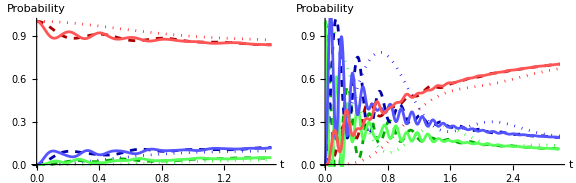

```mathematica
GraphicsGrid[{{Subscript[QutritDiagonalPlot1, R0],Subscript[QutritDiagonalPlot1, R2]},{Lgnd,SpanFromLeft}},Spacings->{1,0},ImageSize->Large]
```

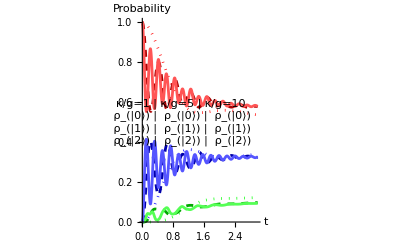

```mathematica
Show[{Subscript[QutritDiagonalPlot1, 0],Graphics[{Inset[Lgnd,{1,0.5}]},Scaled[0.1]]}]
```

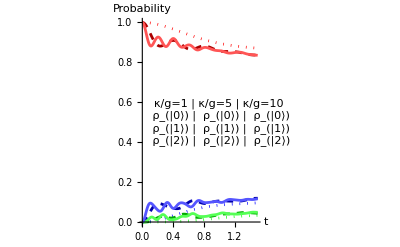

```mathematica
Show[{Subscript[QutritDiagonalPlot1, R0],Graphics[{Inset[Lgnd,{1,0.5}]},Scaled[0.1]]}]
```

### Trace Distance between qutrit states |0⟩ and |2⟩

```mathematica
Subscript[ρSOMatrixMatrix1, ini_,λ_][t_]:=ResourceFunction["MatrixPartialTrace"][Subscript[mat, ini,λ][t][[1]],{1,3},{2,3,2}];
Subscript[MS0Diff, λ_][t_]:=DiagonalMatrix[Diagonal[Subscript[ρSOMatrixMatrix1, 0,λ][t]-Subscript[ρSOMatrixMatrix1, 2,λ][t]]];
Subscript[𝒟, λ_][t_]:=1/2*Tr[MatrixFunction[Sqrt,ConjugateTranspose[Subscript[MS0Diff, λ][t]].Subscript[MS0Diff, λ][t]]]; (*Trace Distance*)
Subscript[TD𝒟, λ_]:=(Subscript[𝒟, λ][t+0.01]-Subscript[𝒟, λ][t])/0.01;
```

```mathematica
Subscript[TD𝒟, 1];
PlotTD1=Plot[%,{t,0,2.5},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["σ(t,ρ_(0, 2)(0))",18.5]},PlotStyle->{RGBColor[0.14,0.8,0.14],Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=1",18.5]},{Right,Top}],ImageSize->Large];
```

```mathematica
Subscript[TD𝒟, 5];
PlotTD5=Plot[%,{t,0,2.5},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["σ(t,ρ_(0, 2)(0))",18.5]},PlotStyle->{RGBColor[0.07,0.25,0.6],Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=5",18.5]},{Right,Top}],ImageSize->Large];
```

```mathematica
Subscript[TD𝒟, 10];
PlotTD10=Plot[%,{t,0,2.5},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["σ(t,ρ_(0, 2)(0))",18.5]},PlotStyle->{Pink,Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=10",18.5]},{Right,Top}],ImageSize->Large];
```

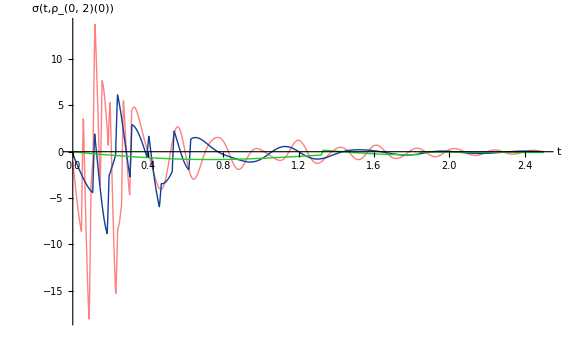

```mathematica
Show[{PlotTD10,PlotTD5,PlotTD1}]
```

```mathematica
InfoBackFlow[ωOL_,ωOR_,ωL_,ωR_,TR_,TL_,intg_,intκ_,unitassum_]:=
Module[{temp,fnRHSρoS0,fnRHSρoS1,fnsol,fndynamicsS1,fndynamicsS0,fnMS0,fnMS1,fnρSOMatrix1,fnρS1Matrix1,fnMSDiff1,fn𝒟1,fnTD1,fnPlotTD1,fnpts1,fnnlm1},
temp=Flatten[{ωassum1,ωassum2,NBEassum,unitassum,Subscript[ω, OL]->ωOL,Subscript[ω, OR]->ωOR,Subscript[ω, L] ->ωL,Subscript[ω, R] ->ωR,Subscript[T, R]->TR*Subscript[ω, R],Subscript[T, L]->TL*Subscript[ω, L],Subscript[g, L]->intg*Subscript[ω, L] ,Subscript[g, R]->intg*Subscript[ω, R],Subscript[κ, L]->intκ*Subscript[g, L],Subscript[κ, R]->intκ*Subscript[g, R]}];
fnRHSρoS0=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S0],Subscript[ρo, R]]//.Flatten[{temp,unitassum}];
fnRHSρoS1=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S2],Subscript[ρo, R]]//.Flatten[{temp,unitassum}];
fnsol=sol//.Flatten[{NBEassum,temp,unitassum,ωassum1}];

fndynamicsS1=NDSolve[Flatten[{fnsol//.Flatten[{NBEassum,temp,unitassum,ωassum1}],N[Table[Subscript[ρ, i,j][0]==fnRHSρoS1[[i,j]],{i,1,12},{j,1,12}]]}],Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}];
fndynamicsS0=NDSolve[Flatten[{fnsol//.Flatten[{NBEassum,temp,unitassum,ωassum1}],N[Table[Subscript[ρ, i,j][0]==fnRHSρoS0[[i,j]],{i,1,12},{j,1,12}]]}],Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}];

fnMS0[t_]:=Table[First[Subscript[ρ, i,j][t]/.fndynamicsS0],{i,1,12},{j,1,12}];
fnMS1[t_]:=Table[First[Subscript[ρ, i,j][t]/.fndynamicsS1],{i,1,12},{j,1,12}];
     fnρSOMatrix1[t_]:=ResourceFunction["MatrixPartialTrace"][fnMS0[t],{1,3},{2,3,2}];
fnρS1Matrix1[t_]:=ResourceFunction["MatrixPartialTrace"][fnMS1[t],{1,3},{2,3,2}];
fnMSDiff1[t_]:=DiagonalMatrix[Diagonal[fnρSOMatrix1[t]-fnρS1Matrix1[t]]];
fn𝒟1[t_]:=1/2*Tr[MatrixFunction[Sqrt,ConjugateTranspose[fnMSDiff1[t]].fnMSDiff1[t]]];
fnTD1=(fn𝒟1[t+0.01]-fn𝒟1[t])/0.01;
fnPlotTD1=Plot[fnTD1,{t,0,5},PlotRange->Full,PlotStyle->Blue,PlotLabel->  Style["κ/g"],AxesLabel->{Style["t(s)"],Style["(ⅆ𝒟 (SubscriptBox[ρ, 1], SubscriptBox[ρ, 2]))/ⅆt"]}];
fnpts1=Cases[fnPlotTD1,Line[dat_]:>dat,All]//Flatten[#,1]&;
fnnlm1=Quiet[NonlinearModelFit[fnpts1,a*Exp[-b*x]*Cos[ω*x+φ]+c,{a,b,ω,φ,c},x]];
{fnnlm1["BestFitParameters"],fnnlm1["EstimatedVariance"],Total[Differences[fnpts1[[All,1]]]*MovingAverage[Clip[fnpts1[[All,2]],{0,∞}],2]]}
]
```

```mathematica
InfoBackFlow[3,3,3,3,0.5,5,0.5,5,unitassum]
```

{{a→4.7544,b→1.727,ω→16.2523,φ→1.18671,c→-0.164317},0.943663,0.630135}

```mathematica
InfoBackFlow[3,3,3,3,0.5,5,0.5,10,unitassum]
```

{{a→8.62316,b→1.91872,ω→-30.8012,φ→4.66603,c→-0.150346},2.54724,1.32071}

```mathematica
InfoBackFlow[3,3,3,3,0.5,5,0.5,1.3,unitassum]
```

{{a→4.38877,b→2.46677,ω→-1.97396,φ→4.79636,c→-0.0560801},0.0239073,0.0336551}

```mathematica
PlotInfoBackFlow[ωOL_,ωOR_,ωL_,ωR_,TR_,TL_,intg_,κmin_,κmax_,κres_,unitassum_]:=
Module[{tempx,tempy,temp,model1},
tempx=Table[{κ},{κ,κmin,κmax,κres}];
tempy=Table[{Abs[InfoBackFlow[ωOL,ωOR,ωL,ωR,TR,TL,intg,intκ,unitassum][[3]]]},{intκ,κmin,κmax,κres}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy[[;;,1]]}]}];
ListPlot[temp,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["κ/g",20],Style["∫_(σ > 0) σ(t,ρ_(0, 2)(0))ⅆt",15]},Joined->True,PlotStyle->{RGBColor[0,0.44,0.44]},ImageSize->Medium]
]
```

```mathematica
(*TotalInfo1=PlotInfoBackFlow[3,3,3,3,0.5,5,0.5,0.01,2.5,0.01,unitassum];*)
```

```mathematica
(*Show[TotalInfo1,Graphics[{Black,Dashed,Line[{{0.83,-0.02},{0.83,0.04}}],Text[Style["κ/g= 0.83",14,Black],{0.83,-0.02},{0,0}]}],PlotRange->{All,{-0.03,0.06}}]*)
```

```mathematica
(*TotalInfo11=PlotInfoBackFlow[3,3,3,3,5,0.5,0.5,1,3,0.01,unitassum];*)
```

```mathematica
(*Show[TotalInfo11,Graphics[{Black,Dashed,Line[{{1.5,-0.02},{1.5,0.04}}],Text[Style["κ/g= 1.5",14,Black],{1.5,-0.02},{0,0}]}],PlotRange->{All,{-0.03,0.06}}]*)
```

### Thermal Flows

Thermal flows from Markovian baths to the system(auxiliary qubits) 
(Q̇)_i=ℏω_B_i g_i^2(⟨σ_B_i^†σ_B_i⟩-(⟨σ_B_i σ_B_i^†⟩+⟨σ_B_i^†σ_B_i⟩)⟨σ_i^†σ_i⟩)

```mathematica
Subscript[dQL, ini_,λ_]:=ℏ*Subscript[ω, L]*Subscript[g, L]^2*(Subscript[n, L][Subscript[ω, L]]-Subscript[ρSLMatrix, ini,λ][[1]])//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
Subscript[dQR, ini_,λ_]:=ℏ*Subscript[ω, R]*Subscript[g, R]^2*(Subscript[n, R][Subscript[ω, R]]-Subscript[ρSRMatrix, ini,λ][[1]])//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
```

```mathematica
Subscript[JQubitO, ini_,λ_]:=Tr[D[Subscript[ρSOMatrixMatrix, ini,λ].HQubit,t]]//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
Subscript[JQubitL, ini_,λ_]:=Tr[D[Subscript[ρSLMatrixMatrix, ini,λ].HLQubit,t]]//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
Subscript[JQubitR, ini_,λ_]:=Tr[D[Subscript[ρSRMatrixMatrix, ini,λ].HRQubit,t]]//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
Subscript[JCombinedSys, ini_,λ_]:=Tr[D[Subscript[mat, ini,λ][t][[1]].Subscript[H, SA],t]]//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
```

### 1) in forward condition

With initial condition 1 - RHSρoS_0

```mathematica
Subscript[JL, 0,1]=Subscript[dQL, 0,1]-Subscript[JQubitL, 0,1];
Subscript[JR, 0,1]=Subscript[dQR, 0,1]-Subscript[JQubitR, 0,1];
Subscript[JL, 0,5]=Subscript[dQL, 0,5]-Subscript[JQubitL, 0,5];
Subscript[JR, 0,5]=Subscript[dQR, 0,5]-Subscript[JQubitR, 0,5];
Subscript[JL, 0,10]=Subscript[dQL, 0,10]-Subscript[JQubitL, 0,10];
Subscript[JR, 0,10]=Subscript[dQR, 0,10]-Subscript[JQubitR, 0,10];
Subscript[JQutrit, 0,1]=Subscript[JQubitO, 0,1];
Subscript[JQutrit, 0,5]=Subscript[JQubitO, 0,5];
Subscript[JQutrit, 0,10]=Subscript[JQubitO, 0,10];
```

```mathematica
Subscript[J1, 0]=Plot[{Subscript[JL, 0,1],Subscript[JR, 0,1]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=1",15],ImageSize->Medium ,PlotRange->All];
Subscript[J5, 0]=Plot[{Subscript[JL, 0,5],Subscript[JR, 0,5]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=5",15],ImageSize->Medium ,PlotRange->All];
Subscript[J10, 0]=Plot[{Subscript[JL, 0,10],Subscript[JR, 0,10]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=10",15],ImageSize->Medium ,PlotRange->All];
```

```mathematica
GraphicsRow[{Subscript[J1, 0],Subscript[J5, 0],Subscript[J10, 0]},ImageSize->Full,Epilog->Inset[Style["Thermal Flows - Forward Condition",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
Subscript[JL, 2,1]=Subscript[dQL, 2,1]-Subscript[JQubitL, 2,1];
Subscript[JR, 2,1]=Subscript[dQR, 2,1]-Subscript[JQubitR, 2,1];
Subscript[JL, 2,5]=Subscript[dQL, 2,5]-Subscript[JQubitL, 2,5];
Subscript[JR, 2,5]=Subscript[dQR, 2,5]-Subscript[JQubitR, 2,5];
Subscript[JL, 2,10]=Subscript[dQL, 2,10]-Subscript[JQubitL, 2,10];
Subscript[JR, 2,10]=Subscript[dQR, 2,10]-Subscript[JQubitR, 2,10];
Subscript[JQutrit, 2,1]=Subscript[JQubitO, 2,1];
Subscript[JQutrit, 2,5]=Subscript[JQubitO, 2,5];
Subscript[JQutrit, 2,10]=Subscript[JQubitO, 2,10];
```

```mathematica
Subscript[J1, 2]=Plot[{Subscript[JL, 2,1],Subscript[JR, 2,1]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=1",15],ImageSize->Medium ,PlotRange->All];
Subscript[J5, 2]=Plot[{Subscript[JL, 2,5],Subscript[JR, 2,5]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=5",15],ImageSize->Medium ,PlotRange->All];
Subscript[J10, 2]=Plot[{Subscript[JL, 2,10],Subscript[JR, 2,10]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=10",15],ImageSize->Medium ,PlotRange->All];
```

```mathematica
GraphicsRow[{Subscript[J1, 2],Subscript[J5, 2],Subscript[J10, 2]},ImageSize->Full,Epilog->Inset[Style["Thermal Flows - Forward Condition - Initial Condition 2",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

### 2) in reverse condition

With initial condition 1 - RHSρoS_0

```mathematica
Subscript[JL, 0,R1]=Subscript[dQL, 0,R1]-Subscript[JQubitL, 0,R1];
Subscript[JR, 0,R1]=Subscript[dQR, 0,R1]-Subscript[JQubitR, 0,R1];
Subscript[JL, 0,R5]=Subscript[dQL, 0,R5]-Subscript[JQubitL, 0,R5];
Subscript[JR, 0,R5]=Subscript[dQR, 0,R5]-Subscript[JQubitR, 0,R5];
Subscript[JL, 0,R10]=Subscript[dQL, 0,R10]-Subscript[JQubitL, 0,R10];
Subscript[JR, 0,R10]=Subscript[dQR, 0,R10]-Subscript[JQubitR, 0,R10];
Subscript[JQutrit, 0,R1]=Subscript[JQubitO, 0,R1];
Subscript[JQutrit, 0,R5]=Subscript[JQubitO, 0,R5];
Subscript[JQutrit, 0,R10]=Subscript[JQubitO, 0,R10];
```

```mathematica
Subscript[JR1, 0]=Plot[{Subscript[JL, 0,R1],Subscript[JR, 0,R1]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=1",15],ImageSize->Medium ,PlotRange->All];
Subscript[JR5, 0]=Plot[{Subscript[JL, 0,R5],Subscript[JR, 0,R5]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=5",15],ImageSize->Medium ,PlotRange->All];
Subscript[JR10, 0]=Plot[{Subscript[JL, 0,R10],Subscript[JR, 0,R10]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=10",15],ImageSize->Medium ,PlotRange->All];
```

```mathematica
GraphicsRow[{Subscript[JR1, 0],Subscript[JR5, 0],Subscript[JR10, 0]},ImageSize->Full,Epilog->Inset[Style["Thermal Flows - Reverse Condition",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
Subscript[JL, 2,R1]=Subscript[dQL, 2,R1]-Subscript[JQubitL, 2,R1];
Subscript[JR, 2,R1]=Subscript[dQR, 2,R1]-Subscript[JQubitR, 2,R1];
Subscript[JL, 2,R5]=Subscript[dQL, 2,R5]-Subscript[JQubitL, 2,R5];
Subscript[JR, 2,R5]=Subscript[dQR, 2,R5]-Subscript[JQubitR, 2,R5];
Subscript[JL, 2,R10]=Subscript[dQL, 2,R10]-Subscript[JQubitL, 2,R10];
Subscript[JR, 2,R10]=Subscript[dQR, 2,R10]-Subscript[JQubitR, 2,R10];
Subscript[JQutrit, 2,R1]=Subscript[JQubitO, 2,R1];
Subscript[JQutrit, 2,R5]=Subscript[JQubitO, 2,R5];
Subscript[JQutrit, 2,R10]=Subscript[JQubitO, 2,R10];
```

```mathematica
Subscript[JR1, 2]=Plot[{Subscript[JL, 2,R1],Subscript[JR, 2,R1]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=1",15],ImageSize->Medium ,PlotRange->All];
Subscript[JR5, 2]=Plot[{Subscript[JL, 2,R5],Subscript[JR, 2,R5]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=5",15],ImageSize->Medium ,PlotRange->All];
Subscript[JR10, 2]=Plot[{Subscript[JL, 2,R10],Subscript[JR, 2,R10]},{t,0,5},AxesStyle->Directive[Darker[Gray],15],AxesLabel->{Style["t",15],Style["Thermal Flows",15]},PlotStyle->{Blue,Red},PlotLegends->Placed[{Style["J_L",13],Style["J_R",13]},Bottom],PlotLabel->Style["κ/g=10",15],ImageSize->Medium ,PlotRange->All];
```

```mathematica
GraphicsRow[{Subscript[JR1, 2],Subscript[JR5, 2],Subscript[JR10, 2]},ImageSize->Full,Epilog->Inset[Style["Thermal Flows - Reverse Condition - Initial Condition 2",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

## Steady State Solutions for density matrices and energy flows

```mathematica
varFunc[ωOL_,ωOR_,ωL_,ωR_,TR_,TL_,intg_,intκ_,unitassum_]:=
Module[{temp0,RHSρoS0,RHSρoS1,temp1,temp2,temp3,mat,ρSLMatrix,ρSRMatrix,dQL,dQR,ρSLMatrixMatrix,ρSRMatrixMatrix,JQubitL,JQubitR,JL,JR},
temp0=Flatten[{ωassum1,ωassum2,NBEassum,unitassum,Subscript[ω, OL]->ωOL,Subscript[ω, OR]->ωOR,Subscript[ω, L] ->ωL,Subscript[ω, R] ->ωR,Subscript[T, R]->TR*Subscript[ω, R],Subscript[T, L]->TL*Subscript[ω, L],Subscript[g, L]->intg*Subscript[ω, L] ,Subscript[g, R]->intg*Subscript[ω, R],Subscript[κ, L]->intκ*Subscript[g, L],Subscript[κ, R]->intκ*Subscript[g, R],λ->intκ}];
RHSρoS0=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S0],Subscript[ρo, R]]//.Flatten[{temp0,unitassum}];
RHSρoS1=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S1],Subscript[ρo, R]]//.Flatten[{temp0,unitassum}];
     temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^12 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]]]]];
mat=Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]//.temp3;
ρSLMatrix=Flatten[ResourceFunction["MatrixPartialTrace"][mat,{2,3},{2,3,2}]];
ρSRMatrix=Flatten[ResourceFunction["MatrixPartialTrace"][mat,{1,2},{2,3,2}]];
dQL=Subscript[g, L]^2*Subscript[ω, L]*(Subscript[n, L][Subscript[ω, L]]-ρSLMatrix[[1]])//.temp0;
dQR=Subscript[g, R]^2*Subscript[ω, R]*(Subscript[n, R][Subscript[ω, R]]-ρSRMatrix[[1]])//.temp0;
ρSLMatrixMatrix=ResourceFunction["MatrixPartialTrace"][mat,{2,3},{2,3,2}];
ρSRMatrixMatrix=ResourceFunction["MatrixPartialTrace"][mat,{1,2},{2,3,2}];
JQubitL=Tr[D[ρSLMatrixMatrix.HLQubit,t]]//.temp0;
JQubitR=Tr[D[ρSRMatrixMatrix.HRQubit,t]]//.temp0;
JL=dQL-JQubitL;
JR=dQR-JQubitR;
Re[{Flatten[Table[Subscript[ρ, i,i],{i,1,12}]/.temp3],{JL,JR}}]]
```

```mathematica
varFunc[3,3,3,3,0.5,5,0.5,1,unitassum]
varFunc[3,3,3,3,5,0.5,0.5,1,unitassum]
```

{{0.00861969,0.0340362,0.026665,0.0958407,0.0356239,0.198019,0.0183807,0.0732038,0.044311,0.179928,0.0369643,0.248407},{0.346692,-0.346692}}

{{0.00350696,0.00743025,0.0111564,0.0197022,0.0415397,0.0554531,0.0140291,0.0292501,0.039392,0.0618556,0.320956,0.395728},{-0.132203,0.132203}}

```mathematica
varFunc[3,3,3,3,0.5,5,0.5,5,unitassum]
varFunc[3,3,3,3,5,0.5,0.5,5,unitassum]
```

{{0.00823278,0.0208084,0.0211074,0.0615745,0.0556503,0.199831,0.0206538,0.0528399,0.0497698,0.197486,0.04675,0.265296},{0.559988,-0.559988}}

{{0.00547082,0.0136409,0.0137505,0.0320785,0.0343124,0.0595259,0.0141445,0.036199,0.037018,0.0604825,0.305894,0.387483},{-0.267139,0.267139}}

```mathematica
varFunc[3,3,3,3,0.5,5,0.5,10,unitassum]
varFunc[3,3,3,3,5,0.5,0.5,10,unitassum]
```

{{0.00809786,0.0203572,0.0205777,0.0589778,0.0574129,0.199838,0.0203445,0.0508937,0.0500791,0.199215,0.0475959,0.266611},{0.573108,-0.573108}}

{{0.00563027,0.0141199,0.0139326,0.0330582,0.0336472,0.0599418,0.0142493,0.0367383,0.0369506,0.0601976,0.304629,0.386905},{-0.277607,0.277607}}

Note: following is only for the sanity check of using local dissipators (steady state heat currents vanish (≈ 0) when T_L=T_R)

```mathematica
varFunc[3,3,3,3,0.5,0.5,0.5,10,unitassum]
varFunc[3,3,3,3,5,5,0.5,10,unitassum]
```

{{0.000225591,0.0016669,0.0016669,0.0123168,0.0123168,0.0910098,0.0016669,0.0123168,0.0123168,0.0910098,0.0910098,0.672477},{9.36751×10^-17,1.8735×10^-16}}

{{0.054575,0.0666581,0.0666581,0.0814163,0.0814163,0.0994422,0.0666581,0.0814163,0.0814163,0.0994422,0.0994422,0.121459},{-3.747×10^-16,-7.49401×10^-16}}

```mathematica
varFunc[3,3,3,3,0.5,0.5,0.5,1,unitassum]
varFunc[3,3,3,3,5,5,0.5,1,unitassum]
```

{{0.000225591,0.0016669,0.0016669,0.0123168,0.0123168,0.0910098,0.0016669,0.0123168,0.0123168,0.0910098,0.0910098,0.672477},{0.,0.}}

{{0.054575,0.0666581,0.0666581,0.0814163,0.0814163,0.0994422,0.0666581,0.0814163,0.0814163,0.0994422,0.0994422,0.121459},{-1.1241×10^-15,-1.8735×10^-15}}

### Plots for adjusting T_L and T_R (at steady state):

### Energy Inflows

```mathematica
varEngyFunc[ωOL_,ωOR_,ωL_,ωR_,TR_,TL_,intg_,intκ_,unitassum_]:=
Module[{temp0,RHSρoS0,RHSρoS1,temp1,temp2,temp3,mat,ρSLMatrix,ρSRMatrix,dQL,dQR,ρSLMatrixMatrix,ρSRMatrixMatrix,JQubitL,JQubitR,JL,JR},
temp0=Flatten[{ωassum1,ωassum2,NBEassum,unitassum,Subscript[ω, OL]->ωOL,Subscript[ω, OR]->ωOR,Subscript[ω, L] ->ωL,Subscript[ω, R] ->ωR,Subscript[T, R]->TR*Subscript[ω, R],Subscript[T, L]->TL*Subscript[ω, L],Subscript[g, L]->intg*Subscript[ω, L] ,Subscript[g, R]->intg*Subscript[ω, R],Subscript[κ, L]->intκ*Subscript[g, L],Subscript[κ, R]->intκ*Subscript[g, R],λ->intκ}];
RHSρoS0=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S0],Subscript[ρo, R]]//.Flatten[{temp0,unitassum}];
RHSρoS1=KroneckerProduct[Subscript[ρo, L],Subscript[ρo, S1],Subscript[ρo, R]]//.Flatten[{temp0,unitassum}];
     temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^12 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]]]]];
mat=Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]//.temp3;
ρSLMatrix=Flatten[ResourceFunction["MatrixPartialTrace"][mat,{2,3},{2,3,2}]];
ρSRMatrix=Flatten[ResourceFunction["MatrixPartialTrace"][mat,{1,2},{2,3,2}]];
dQL=Subscript[g, L]^2*Subscript[ω, L]*(Subscript[n, L][Subscript[ω, L]]-ρSLMatrix[[1]])//.temp0;
dQR=Subscript[g, R]^2*Subscript[ω, R]*(Subscript[n, R][Subscript[ω, R]]-ρSRMatrix[[1]])//.temp0;
ρSLMatrixMatrix=ResourceFunction["MatrixPartialTrace"][mat,{2,3},{2,3,2}];
ρSRMatrixMatrix=ResourceFunction["MatrixPartialTrace"][mat,{1,2},{2,3,2}];
JQubitL=Tr[D[ρSLMatrixMatrix.HLQubit,t]]//.temp0;
JQubitR=Tr[D[ρSRMatrixMatrix.HRQubit,t]]//.temp0;
JL=dQL-JQubitL;
JR=dQR-JQubitR;
Re[{JL,JR}]]
```

```mathematica
PlotEngyFlowsWithTLTR[Tmin_,Tmax_,Tres_,Tfix_,ωOL_,ωOR_,ωL_,ωR_,intg_,intκ_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=Table[varEngyFunc[ωOL,ωOR,ωL,ωR,Tfix,TL,intg,intκ,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=Table[varEngyFunc[ωOL,ωOR,ωL,ωR,TR,Tfix,intg,intκ,unitassum],{TR,Tmin,Tmax,Tres}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}],MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]}];
ListPlot[temp,AxesOrigin->{0,0},AxesLabel->{"T","J_L"},Joined->True,PlotStyle->{{Thickness->Large,Purple},{Thickness->Large,Pink}},PlotLegends->{"T_L=T,T_R=0.5","T_L=0.5,T_R=T"},PlotRange->All,ImageSize->Medium,PlotLabel->  Style["κ/g=" <> ToString[intκ]]]]
```

```mathematica
Plot1=PlotEngyFlowsWithTLTR[0.05,3,0.05,0.5,3,3,3,3,0.5,1];
Plot2=PlotEngyFlowsWithTLTR[0.05,3,0.05,0.5,3,3,3,3,0.5,5];
Plot3=PlotEngyFlowsWithTLTR[0.05,3,0.05,0.5,3,3,3,3,0.5,10];
```

```mathematica
GraphicsRow[{Plot1,Plot2,Plot3},ImageSize->Full,Epilog->Inset[Style["Steady State Thermal Flows",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

-Graphics-

```mathematica
PlotEngyFlowsWithTemCoupFB[Tmin_,Tmax_,Tres_,Tfix_,ωOL_,ωOR_,ωL_,ωR_,intg_,κmin_,κmax_,κres_]:= 
Module[{tempx,tempy,tempz1,tempz2,temp},
tempx=Table[T,{T,Tmin,Tmax,Tres},{κ,κmin,κmax,κres}];
tempy=Table[κ,{T,Tmin,Tmax,Tres},{κ,κmin,κmax,κres}];
tempz1=Table[varEngyFunc[ωOL,ωOR,ωL,ωR,Tfix,TL,intg,intκ,unitassum][[1]],{TL,Tmin,Tmax,Tres},{intκ,κmin,κmax,κres}];
temp=Flatten[Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]],tempz1[[;;,i]]}],{i,1,Dimensions[tempy][[2]]}],1];
min=Min[tempz1];
max=Max[tempz1];
ListPlot3D[temp,AxesOrigin->{0,0},AxesLabel->{Style["T_L",FontSize->13],Style["κ/g",FontSize->13],Style["J_L(J_R)",FontSize->13]},ColorFunction->"LakeColors",PlotRange->All,ImageSize->Medium,Axes->{True,True,True},PlotLegends->Placed[BarLegend[{"LakeColors",{min,max}}],Bottom],Mesh->None,BoundaryStyle->Directive[LightGray,Thin]]]
```

```mathematica
(*ssflowplotFB=PlotEngyFlowsWithTemCoupFB[0.05,3,0.05,0.5,3,3,3,3,0.5,0.01,5,1];*)
```

```mathematica
(*Show[{ssflowplotFB,Graphics3D[{Gray,Opacity[0.3],EdgeForm[],HalfPlane[{{0,0.83,0},{3,0.83,0}},{0,0,5}]}]}] (*remove this comment to generate following figure*)*)
```

```mathematica
-Graphics3D-;
```

```mathematica
PlotEngyFlowsWithTemCoupRB[Tmin_,Tmax_,Tres_,Tfix_,ωOL_,ωOR_,ωL_,ωR_,intg_,κmin_,κmax_,κres_]:= 
Module[{tempx,tempy,tempz1,tempz2,temp},
tempx=Table[T,{T,Tmin,Tmax,Tres},{κ,κmin,κmax,κres}];
tempy=Table[κ,{T,Tmin,Tmax,Tres},{κ,κmin,κmax,κres}];
tempz2=Table[Abs[varEngyFunc[ωOL,ωOR,ωL,ωR,TR,Tfix,intg,intκ,unitassum][[1]]],{TR,Tmin,Tmax,Tres},{intκ,κmin,κmax,κres}];
temp=Flatten[Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]],tempz2[[;;,i]]}],{i,1,Dimensions[tempy][[2]]}],1];
min=Min[tempz2];
max=Max[tempz2];
ListPlot3D[temp,AxesOrigin->{0,0},AxesLabel->{Style["T_R",FontSize->13],Style["κ/g",FontSize->13],Style["J_L(J_R)",FontSize->13]},ColorFunction->"ValentineTones",PlotRange->All,ImageSize->Medium,Axes->{True,True,True},PlotLegends->Placed[BarLegend[{"ValentineTones",{min,max}}],Bottom],Mesh->None,BoundaryStyle->Directive[LightGray,Thin]]]
```

```mathematica
(*ssflowplotRB=PlotEngyFlowsWithTemCoupRB[0.05,3,0.05,0.5,3,3,3,3,0.5,1,5,1];
Show[{ssflowplotRB,Graphics3D[{Gray,Opacity[0.3],EdgeForm[],HalfPlane[{{0,1.5,0},{3,1.5,0}},{0,0,1}]}]}] (*remove this comment to generate following figure*)*)
```

```mathematica
-Graphics3D-;
```

### Rectification Factor

```mathematica
PlotRecFacWithTL[Tmin_,Tmax_,Tres_,Tfix_,ωOL_,ωOR_,ωL_,ωR_,intg_,intκ_]:= 
Module[{tempx,tempy1,tempy2,temp,temp1,temp2},
tempy1=Table[varEngyFunc[ωOL,ωOR,ωL,ωR,Tfix,TL,intg,intκ,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=Table[varEngyFunc[ωOL,ωOR,ωL,ωR,TR,Tfix,intg,intκ,unitassum],{TR,Tmin,Tmax,Tres}];
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
Size=Length[tempx];
temp=Table[MapThread[List,{tempx[[;;,1]],Abs[tempy1[[;;,1]]],Abs[tempy2[[;;,1]]]}]];
temp1=Table[Max[temp[[i,2]],temp[[i,3]]],{i,1,Size}];
temp2=Table[MapThread[List,{tempx[[;;,1]],(Abs[(tempy1[[;;,1]]+tempy2[[;;,1]])])/temp1}]]]
```

```mathematica
Subscript[RecPlot1, 1]=ListLogLinearPlot[PlotRecFacWithTL[0.05,0.5-0.01,0.01,0.5,3,3,3,3,0.5,1],AxesLabel->{Style["T_L",FontSize->13],Style["R(T_L,T_R=0.5ℏω_R/k_B)",13]},Joined->True,PlotStyle->{Thickness->Large,Green},PlotRange->{{0.05,5},{-0.1,1.1}},ImageSize->Medium];
Subscript[RecPlot2, 1]=ListLogLinearPlot[PlotRecFacWithTL[0.5+0.01,5,0.01,0.5,3,3,3,3,0.5,1],AxesLabel->{Style["T_L",FontSize->13],Style["R(T_L,T_R=0.5ℏω_R/k_B)",13]},Joined->True,PlotStyle->{Thickness->Large,Green},PlotRange->{{0.05,5},{-0.1,1.1}},PlotLegends-> Placed[{Style["κ/g=1",13]},{Right,Top}],ImageSize->Medium];
Subscript[RectificationPlot, 1]=Show[Subscript[RecPlot1, 1],Subscript[RecPlot2, 1]];
```

```mathematica
Subscript[RecPlot1, 5]=ListLogLinearPlot[PlotRecFacWithTL[0.05,0.5-0.01,0.01,0.5,3,3,3,3,0.5,5],AxesLabel->{Style["T_L",FontSize->13],Style["R(T_L,T_R=0.5ℏω_R/k_B)",13]},Joined->True,PlotStyle->{Thickness->Large,RGBColor[0.07,0.25,0.6],Dashed},PlotRange->{{0.05,5},{-0.1,1.1}},ImageSize->Medium];
Subscript[RecPlot2, 5]=ListLogLinearPlot[PlotRecFacWithTL[0.5+0.01,5,0.01,0.5,3,3,3,3,0.5,5],AxesLabel->{Style["T_L",FontSize->13],Style["R(T_L,T_R=0.5ℏω_R/k_B)",13]},Joined->True,PlotStyle->{Thickness->Large,RGBColor[0.07,0.25,0.6],Dashed},PlotRange->{{0.05,5},{-0.1,1.1}},PlotLegends-> Placed[{Style["κ/g=5",13]},{Right,Top}],ImageSize->Medium];
Subscript[RectificationPlot, 5]=Show[Subscript[RecPlot1, 5],Subscript[RecPlot2, 5]];
```

```mathematica
Subscript[RecPlot1, 10]=ListLogLinearPlot[PlotRecFacWithTL[0.05,0.5-0.01,0.01,0.5,3,3,3,3,0.5,10],AxesLabel->{Style["T_L",FontSize->13],Style["R(T_L,T_R=0.5ℏω_R/k_B)",13]},Joined->True,PlotStyle->{Thickness->Large,RGBColor[0.93,0.27,0.27],Dotted},PlotRange->{{0.05,5},{-0.1,1.1}},ImageSize->Medium];
Subscript[RecPlot2, 10]=ListLogLinearPlot[PlotRecFacWithTL[0.5+0.01,5,0.01,0.5,3,3,3,3,0.5,10],AxesLabel->{Style["T_L",FontSize->13],Style["R(T_L,T_R=0.5ℏω_R/k_B)",13]},Joined->True,PlotStyle->{Thickness->Large,RGBColor[0.93,0.27,0.27],Dotted},PlotRange->{{0.05,5},{-0.1,1.1}},PlotLegends-> Placed[{Style["κ/g=10",13]},{Right,Top}],ImageSize->Medium];
Subscript[RectificationPlot, 10]=Show[Subscript[RecPlot1, 10],Subscript[RecPlot2, 10]];
```

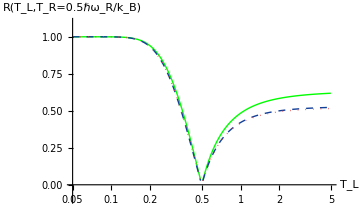

```mathematica
Show[{Subscript[RectificationPlot, 1],Subscript[RectificationPlot, 5],Subscript[RectificationPlot, 10]},ImageSize->Medium]
```